```mathematica
SetDirectory[NotebookDirectory[]];
```

# New full model

## Swept of different initial metallicity values for the new full model (based on the self consistent Ascasibar et al. model, and with variable τ_S).

## Constants

```mathematica
KK=1/400; (*[(M_(\[PermutationProduct]))^(-2/3) pc^(4/3) Gyr^-1]*)
R=18/100;
ηion=95529/100;
ηdiss=38093/100;
C1=303/100000000; (*[Gyr]*)
C2=874/10000000; (*[Gyr]*)
Zsun=134/10000;
Zsn=9/100;
Zeff=Zsun*10^-3;
```

## Auxiliary function

```mathematica
g=i[t]+a[t]+m[t];
tot=g+s[t];
τS=KK^-1*m[t]^(1/3)*g^(-1/3)*tot^(-2/3);
ψ=m[t]/τS;
Z=z[t]/g;
τR=C1/i[t];
τC=C2/(a[t]+m[t])*1/(Z+Zeff);
```

## ODE system

### Initial conditions and parameters for test run and time measurement

```mathematica
g0=10000;(*[M_(\[PermutationProduct]) pc^-3]*)
i0=g0*1/1000;(*[M_(\[PermutationProduct]) pc^-3]*)
a0=g0*500/1000;(*[M_(\[PermutationProduct]) pc^-3]*)
m0=g0*499/1000;(*[M_(\[PermutationProduct]) pc^-3]*)
s0=g0*0;(*[M_(\[PermutationProduct]) pc^-3]*)
z0=g0*zf0;(*[M_(\[PermutationProduct]) pc^-3]*)
Ini={i0,a0,m0,s0,z0};
```

```mathematica
Tstart=0; (*[Gyr]*)
Tend=1; (*[Gyr]*)
```

### System

```mathematica
var={i[t],a[t],m[t],s[t],z[t]};
equ = {
i'[t]==-i[t]/τR+(ηion+R)*ψ,
a'[t]==-a[t]/τC+i[t]/τR+(ηdiss-ηion)*ψ,
m'[t]==a[t]/τC-ηdiss*ψ-ψ,
s'[t]==(1-R)*ψ,
z'[t]==(Zsn*R-Z)*ψ,
i[Tstart]==i0,
a[Tstart]==a0,
m[Tstart]==m0,
s[Tstart]==s0,
z[Tstart]==z0
};
```

## Calculate and save solution in file

```mathematica
Zf0=Table[i,{i,0,0.03,0.0005}];
```

```mathematica
stellarF=Table[
sol=NDSolve[N[equ,60],var,{t,Tstart,Tend}][[1]];
star=s[t]/.sol;
(star/g0)/.t->1,
{zf0,Zf0}]
```

{0.613178,0.613416,0.613454,0.613476,0.613492,0.613504,0.613515,0.613523,0.61353,0.613537,0.613542,0.613548,0.613552,0.613556,0.61356,0.613564,0.613567,0.61357,0.613573,0.613576,0.613578,0.613581,0.613583,0.613585,0.613587,0.613589,0.613591,0.613592,0.613594,0.613595,0.613597,0.613598,0.6136,0.613601,0.613602,0.613603,0.613605,0.613606,0.613607,0.613608,0.613609,0.61361,0.613611,0.613612,0.613612,0.613613,0.613614,0.613615,0.613616,0.613616,0.613617,0.613618,0.613619,0.613619,0.61362,0.61362,0.613621,0.613622,0.613622,0.613623,0.613623}

```mathematica
result=MapThread[{#1,#2}&,{Zf0,stellarF}];
```

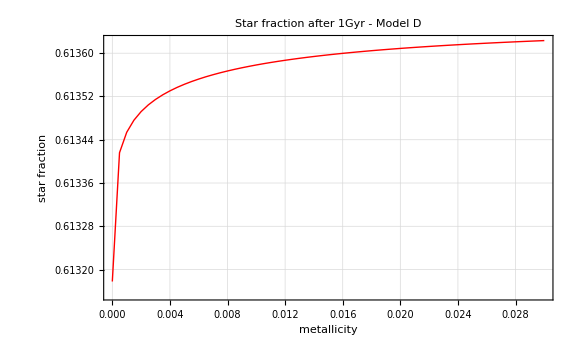

```mathematica
ListPlot[result,
Joined->True,
PlotStyle->{Thick,Red},
FrameLabel->{Style["metallicity",18],Style["star fraction",18] },
FrameStyle->Directive[Black,15],
ImageSize->Large,
Frame->True,
PlotRange->All,
GridLines->Automatic,
PlotLabel->Style["Star fraction after 1Gyr - Model D",20,Bold,Black]]
```